# Shopzilla Bayesian Result Analysis

## Read Data

```mathematica
raw = ReadList["D:/data/bayesian_classification_res.txt",{Real,Real,Real,Number}];
raw = ReadList["D:/data/crawled_crossv_res.txt",{Real,Real,Real,Number}];
```

```mathematica
data = {#[[1]]-#[[2]],#[[2]]-#[[3]],Rationalize[#[[4]]]}&/@raw;
```

```mathematica
data[[1;;10]]
```

{{0.121295,12.5267,1},{18.6761,5.822,1},{23.6655,2.30872,1},{30.8803,4.01104,1},{62.2254,0.859236,1},{51.5415,10.864,1},{28.0348,10.0706,1},{52.5275,16.5068,1},{41.9587,19.1683,1},{32.2435,13.4419,1}}

```mathematica
Length[data]
```

278410

```mathematica
cates=SortBy[GatherBy[data,Last],#[[1,3]]&];
```

```mathematica
cates1=SortBy[GatherBy[data,Last[#]<2&],#[[1,3]]&];
```

```mathematica
cates2=SortBy[GatherBy[data,Last[#]<3&],#[[1,3]]&];
```

```mathematica
cates2=SortBy[GatherBy[data,Last[#]<3&],#[[1,3]]&];
```

```mathematica
Length[cates]
```

4

```mathematica
Dimensions[cates]
```

{4}

```mathematica
#[[1,3]]&/@cates
```

{1,2,3,4}

```mathematica
Tally[Last/@data]
```

{{2,7208},{1,263178},{4,5939},{3,2085}}

## Plot 4 categories

```mathematica
ListPlot[cates[[1,;;,1;;2]], PlotLegends->Automatic]
```

-Graphics-

```mathematica
ListPlot[cates[[;;,;;,1;;2]], PlotLegends->Automatic]
```

-Graphics-

```mathematica
Show[ListPlot[cates2[[;;,;;,1;;2]], PlotLegends->Automatic,PlotStyle->{Blue,{Red,PointSize[Large]}}],Plot[-0.37911359/0.43093261 x+1.14922047/0.43093261,{x,0,5}]]
```

-Graphics-

```mathematica
ListPlot[cates1[[;;,;;,1;;2]], PlotLegends->Automatic,PlotStyle->{Blue,{Red,PointSize[Large]}}]
```

-Graphics-

```mathematica
Show[SmoothHistogram3D[cates1[[1,;;,1;;2]], ColorFunction->"TemperatureMap",PlotRange->{{0,50},{0,50}}],SmoothHistogram3D[cates1[[2,;;,1;;2]], ColorFunction->"DeepSeaColors"]]
```

```mathematica
Show[SmoothHistogram3D[cates2[[1,;;,1;;2]], ColorFunction->"TemperatureMap",PlotRange->{{0,50},{0,50}}],SmoothHistogram3D[cates2[[2,;;,1;;2]], ColorFunction->"DeepSeaColors"]]
```

-Graphics3D-

## ROC Ploting

```mathematica
Length[cates1]
```

2

```mathematica
Length/@cates1
```

{263178,15232}

```mathematica
Length/@cates2
```

{270386,8024}

```mathematica
Length[cates1[[2]]]/Length[data]//N
```

0.0547107

```mathematica
roc1=Table[(Function[l,Length[Select[l,#[[1]]>i&]]]/@cates1)/{263178,15232}//N//Reverse,{i,0,50}];
```

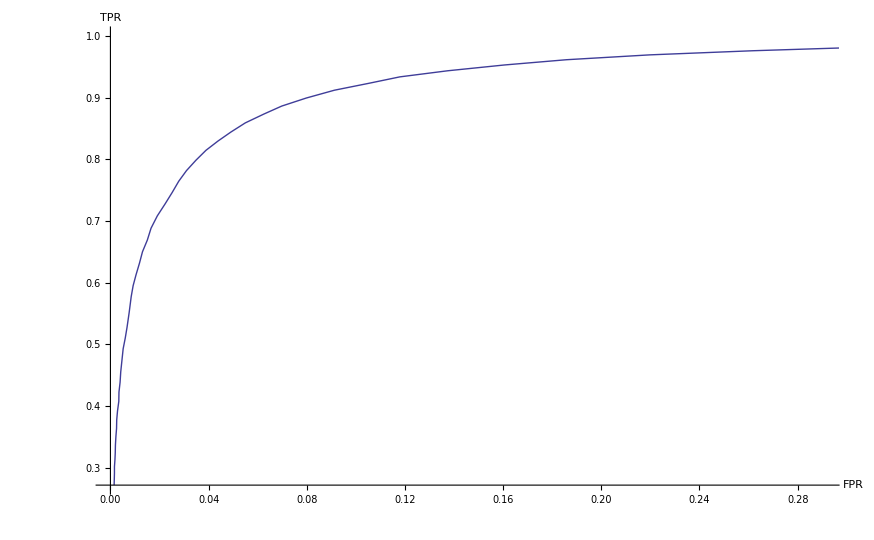

```mathematica
ListPlot[roc1,Joined->True,AxesLabel->{"FPR","TPR"}]
```

```mathematica
Prepend[Transpose[roc1],Range[0,50]]//Transpose//TableForm
```

0 | 1. | 1.
1 | 0.381237 | 0.987624
2 | 0.30994 | 0.982138
3 | 0.261686 | 0.976058
4 | 0.2198 | 0.969393
5 | 0.185793 | 0.961505
6 | 0.160583 | 0.953017
7 | 0.137408 | 0.94359
8 | 0.11791 | 0.933699
9 | 0.105173 | 0.923177
10 | 0.0912553 | 0.912079
11 | 0.0798319 | 0.899444
12 | 0.0697873 | 0.886343
13 | 0.0625 | 0.873382
14 | 0.0549501 | 0.859092
15 | 0.0491071 | 0.844314
16 | 0.043855 | 0.829758
17 | 0.0389312 | 0.81465
18 | 0.0348608 | 0.798642
19 | 0.0309874 | 0.781722
20 | 0.0278361 | 0.764513
21 | 0.0251444 | 0.746141
22 | 0.0222558 | 0.727637
23 | 0.0191045 | 0.708334
24 | 0.0165441 | 0.688298
25 | 0.0150341 | 0.669053
26 | 0.0130646 | 0.650172
27 | 0.0118172 | 0.631386
28 | 0.0104386 | 0.612893
29 | 0.00925683 | 0.595266
30 | 0.00846901 | 0.577506
31 | 0.00761555 | 0.551007
32 | 0.00676208 | 0.527498
33 | 0.00603992 | 0.510202
34 | 0.00518645 | 0.492857
35 | 0.00472689 | 0.475431
36 | 0.00420168 | 0.455433
37 | 0.00393908 | 0.438631
38 | 0.00347952 | 0.42257
39 | 0.00341387 | 0.40761
40 | 0.00288866 | 0.392035
41 | 0.0025604 | 0.377482
42 | 0.00249475 | 0.363689
43 | 0.00223214 | 0.350561
44 | 0.00203519 | 0.336726
45 | 0.00196954 | 0.324309
46 | 0.00183824 | 0.3128
47 | 0.00164128 | 0.30172
48 | 0.00164128 | 0.291301
49 | 0.00157563 | 0.281536
50 | 0.00150998 | 0.271786

```mathematica
roc2=Table[(Function[l,Length[Select[l,#[[2]]>i-0.8797514534813228#[[1]]&]]]/@cates2)/{270386,8024}//N//Reverse,{i,0,15,0.3}];
```

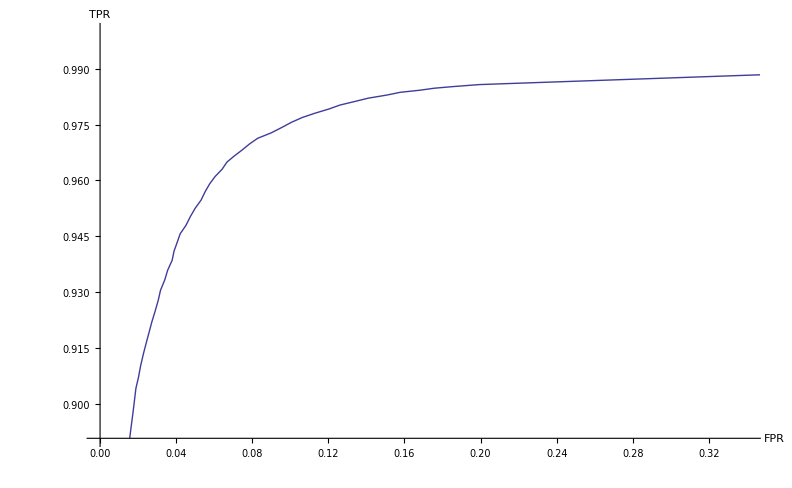

```mathematica
ListPlot[roc2,Joined->True,AxesLabel->{"FPR","TPR"}]
```

```mathematica
Prepend[Transpose[roc2],Range[0,15,0.3]]//Transpose//TableForm
```

0. | 1. | 1.
0.3 | 0.996137 | 0.999959
0.6 | 0.217722 | 0.986087
0.9 | 0.199277 | 0.985754
1.2 | 0.185942 | 0.985236
1.5 | 0.175723 | 0.984785
1.8 | 0.167871 | 0.98423
2.1 | 0.157777 | 0.983683
2.4 | 0.150673 | 0.982936
2.7 | 0.140952 | 0.982107
3. | 0.133848 | 0.981208
3.3 | 0.126122 | 0.980262
3.6 | 0.120389 | 0.979211
3.9 | 0.113036 | 0.978076
4.2 | 0.106306 | 0.976922
4.5 | 0.100573 | 0.975613
4.8 | 0.0954636 | 0.974218
5.1 | 0.0898554 | 0.972761
5.4 | 0.0828764 | 0.971334
5.7 | 0.0786391 | 0.969839
6. | 0.074651 | 0.968168
6.3 | 0.0704138 | 0.966518
6.6 | 0.066675 | 0.964921
6.9 | 0.0641825 | 0.963034
7.2 | 0.0604437 | 0.961041
7.5 | 0.0575773 | 0.959055
7.8 | 0.0552094 | 0.956954
8.1 | 0.0530907 | 0.954709
8.4 | 0.0499751 | 0.952512
8.7 | 0.0474826 | 0.950315
9. | 0.0451147 | 0.9479
9.3 | 0.0421236 | 0.945681
9.6 | 0.0405035 | 0.943322
9.9 | 0.0388833 | 0.940995
10.2 | 0.0378863 | 0.938536
10.5 | 0.0355184 | 0.935858
10.8 | 0.0340229 | 0.933295
11.1 | 0.0317797 | 0.930499
11.4 | 0.0305334 | 0.927703
11.7 | 0.0289133 | 0.924819
12. | 0.0271685 | 0.921901
12.3 | 0.0257976 | 0.919256
12.6 | 0.0243021 | 0.916401
12.9 | 0.0228066 | 0.913453
13.2 | 0.0213111 | 0.910184
13.5 | 0.0201894 | 0.907081
13.8 | 0.0188185 | 0.904074
14.1 | 0.0180708 | 0.900857
14.4 | 0.017323 | 0.897694
14.7 | 0.0164506 | 0.894233
15. | 0.0155783 | 0.890701

```mathematica
{1.0,0.14} 8024/270386
```

{0.0296761,0.00415465}